## Potential solutions (Poisson)

```mathematica
(*outer*)ϕ3[r_]:=(λD BesselK[0,r/λD] (ϵ2 λD (R1 σ1+R2 σ2) BesselI[0,R1/λD]+R1 R2 ϵ σ2 BesselI[1,R1/λD] Log[R2/R1]))/(R2 ϵ ϵ2 λD BesselI[0,R1/λD] BesselK[1,R2/λD]+R1 ϵ BesselI[1,R1/λD] (ϵ2 λD BesselK[0,R2/λD]+R2 ϵ BesselK[1,R2/λD] Log[R2/R1]));
```

```mathematica
(*inner*)ϕ1[r_]:=(λD BesselI[0,r/λD] (ϵ2 λD (R1 σ1+R2 σ2) BesselK[0,R2/λD]+R1 R2 ϵ σ1 BesselK[1,R2/λD] Log[R2/R1]))/(R2 ϵ ϵ2 λD BesselI[0,R1/λD] BesselK[1,R2/λD]+R1 ϵ BesselI[1,R1/λD] (ϵ2 λD BesselK[0,R2/λD]+R2 ϵ BesselK[1,R2/λD] Log[R2/R1]));
```

```mathematica
ϕ2[r_]:=(R1 R2 ϵ λD σ2 BesselI[1,R1/λD] BesselK[0,R2/λD] Log[r/R1]+λD BesselI[0,R1/λD] (ϵ2 λD (R1 σ1+R2 σ2) BesselK[0,R2/λD]+R1 R2 ϵ σ1 BesselK[1,R2/λD] (-Log[r/R1]+Log[R2/R1])))/(R2 ϵ ϵ2 λD BesselI[0,R1/λD] BesselK[1,R2/λD]+R1 ϵ BesselI[1,R1/λD] (ϵ2 λD BesselK[0,R2/λD]+R2 ϵ BesselK[1,R2/λD] Log[R2/R1]));
```

## Parameters

```mathematica
R2=12.5*^-9
```

1.25×10^-8

```mathematica
R1=7.5*^-9
```

7.5×10^-9

```mathematica
ϵ0=N[QuantityMagnitude[UnitConvert[Quantity["ElectricConstant"],"SIBase"]]]
```

8.85419×10^-12

```mathematica
ϵ=9*ϵ0
```

7.96877×10^-11

```mathematica
ϵ2=2*ϵ0
```

1.77084×10^-11

```mathematica
(*R = QuantityMagnitude[UnitConvert[Quantity["GasConstant"],"SIBase"]]*)
```

```mathematica
R=8.314462618  (*J/(mol*K)*)
```

8.31446

```mathematica
F=QuantityMagnitude[UnitConvert[Quantity["FaradayConstant"],"SIBase"]]
```

120606665154137523/1250000000000

```mathematica
T=310
```

310

```mathematica
iccc1bulk=140;    (* K+ ------->140 mM = 140 mol/m^3 *)
iccc2bulk=12;    (* Na+ ------->12 mM = 12 mol/m^3 *)
iccc3bulk=4;    (* Cl- ------->4 mM = 4 mol/m^3 *)
iccc4bulk=74;    (* HPO4(-2) ------->74 mM = 74 mol/m^3 *)

(*Charge number of the species - Ion Valency*)
z1=1;  (* K+ *)
z2=1; (* Na+ *)
z3=-1; (* Cl- *)
z4=-2;(* HPO4(-2) *)
```

```mathematica
λD=Sqrt[ϵ *R*T/F^2/(z1^2*iccc1bulk+z2^2*iccc2bulk+z3^2*iccc3bulk+z4^2*iccc4bulk)]
```

2.20934×10^-10

```mathematica
σ1=-0.025(*C/m^2*)
```

-0.025

```mathematica
σ2=-0.083(*C/m^2*)
```

-0.083

## Plot

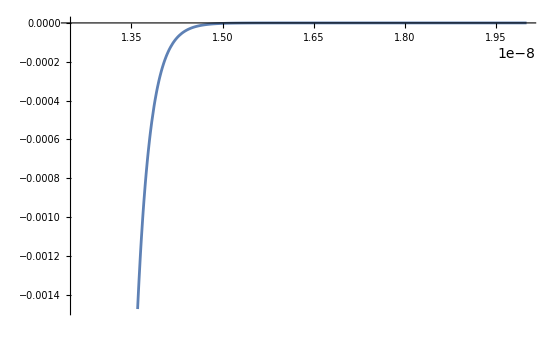

```mathematica
p3=Plot[ϕ3[r],{r,12.5*^-9,20*^-9}]
```

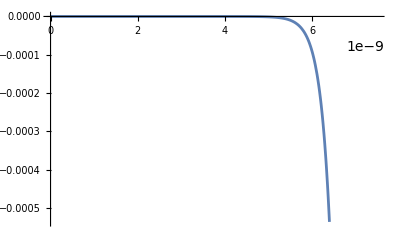

```mathematica
p1=Plot[ϕ1[r],{r,0,7.5*^-9}]
```

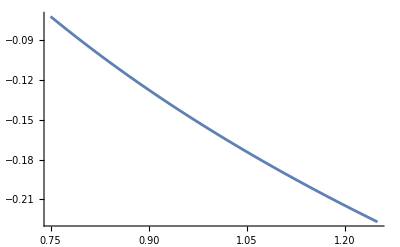

```mathematica
p2=Plot[ϕ2[r],{r,7.5*^-9,12.5*^-9}]
```

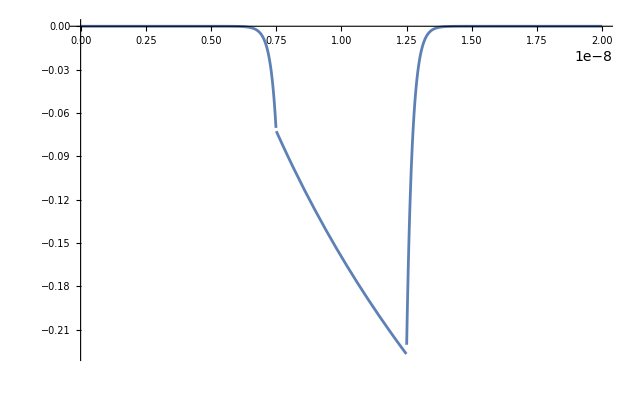

```mathematica
Plot[Piecewise[{{ϕ1[r],r<=R1},{ϕ2[r],R1<=r<=R2},{ϕ3[r],r>=R2}}],{r,0,20*^-9}]
```

## Rl

```mathematica
l=8*^-9
```

1/125000000

```mathematica
(* Mobility of the species [mol.m^2/(J.s)]*)
u1=7.898*^-13;  (* K+ *)
u2=5.384*^-13; (* Na+ *)
u3=8.2011*^-13; (* Cl- *)
u4=7.089*^-13; (* HPO4(-2) *)
```

```mathematica
G=F^2*(z1^2*u1*iccc1bulk+z2^2*u2*iccc2bulk+z3^2*u3*iccc3bulk+z4^2*u4*iccc4bulk)
```

3.07348

```mathematica
e=1.602176634*10^-19  (*Elementary charge in Coulombs*)
```

1.60218×10^-19

```mathematica
(*e=QuantityMagnitude[UnitConvert[Quantity["FundamentalCharge"],"SIBase"]]*)
```

```mathematica
Kb=QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"],"SIBase"]]
```

1380649/100000000000000000000000000000

```mathematica
lb=e^2/(4*π*ϵ*Kb*T)
```

5.98928×10^-9

```mathematica
μ=0.00089
```

0.00089

```mathematica
H=F^3/(R*T)*(z1^3*u1*iccc1bulk+z2^3*u2*iccc2bulk+z3^3*u3*iccc3bulk+z4^3*u4*iccc4bulk)
```

-106.608

```mathematica
L=BesselK[0,R2/λD]
```

4.45972×10^-26

```mathematica
ddD=(λD (ϵ2 λD (R1 σ1+R2 σ2) BesselI[0,R1/λD]^2+R1 R2 ϵ σ2 BesselI[1,R1/λD] Log[R2/R1]))/(R2 ϵ ϵ2 λD BesselI[0,R1/λD]^2 BesselK[1,R2/λD]+R1 ϵ BesselI[1,R1/λD] (ϵ2 λD BesselK[0,R2/λD]+R2 ϵ BesselK[1,R2/λD] Log[R2/R1]))
```

-6.03929×10^24

```mathematica
Rl=Abs[l/(π (G lb (lb+2 R2)-2 ddD H R2 λD BesselK[1,R2/λD]+2 ddD H (lb+R2) λD BesselK[1,(lb+R2)/λD]+1/(λD μ)ddD^2 ϵ^2 (R2^2 BesselK[0,R2/λD]^2-(lb+R2)^2 BesselK[0,(lb+R2)/λD]^2+(2 L λD-R2 BesselK[1,R2/λD]-(lb+R2) BesselK[1,(lb+R2)/λD]) (R2 BesselK[1,R2/λD]-(lb+R2) BesselK[1,(lb+R2)/λD]))))]
```

6.20397×10^6

## ρl

```mathematica
aaA=(λD (ϵ2 λD (R1 σ1+R2 σ2) BesselK[0,R2/λD]+R1 R2 ϵ σ1 BesselK[1,R2/λD] Log[R2/R1]))/(R2 ϵ ϵ2 λD BesselI[0,R1/λD] BesselK[1,R2/λD]+R1 ϵ BesselI[1,R1/λD] (ϵ2 λD BesselK[0,R2/λD]+R2 ϵ BesselK[1,R2/λD] Log[R2/R1]))
```

-1.90336×10^-15

```mathematica
M=BesselI[0,R1/λD]
```

3.80208×10^13

```mathematica
ρl=Abs[(l λD μ)/(π(-G lb (lb-2 R1) λD μ+aaA (-aaA (lb-R1)^2 ϵ^2 BesselI[0,(lb-R1)/λD]^2+aaA R1^2 ϵ^2 BesselI[0,R1/λD]^2+((lb-R1) BesselI[1,(lb-R1)/λD]-R1 BesselI[1,R1/λD]) (2 λD (aaA M ϵ^2+H λD μ)+aaA ϵ^2 ((lb-R1) BesselI[1,(lb-R1)/λD]+R1 BesselI[1,R1/λD])))))]
```

1.81011×10^7